```mathematica
coeff[n_,k_]:=If[k<=n,Binomial[n,k](1-η)^k η^(n-k),0](*If[k<=n,Binomial[n,k](1-η)^(n-k)η^k,0]*)
```

```mathematica
summand[n_,l_]:=2(l+1)(coeff[n,l]-coeff[n,l+1])^2/(coeff[n,l]+coeff[n,l+1])
```

```mathematica
QFI[n_(*?NumericQ*)]:=Sum[summand[n,l],{l,0,n}](*TODO: add N[...,precision]*)
```

```mathematica
QFI[n]
```

$Aborted

```mathematica
%//Reduce
```

Reduce::naqs: ∑_(l=0)^n (2 (1+l) (If[l≤n,Binomial[n,l] Plus[«2»]^Plus[«2»] η^l,0]-If[«1»])^2)/(If[l≤n,Binomial[n,l] Plus[«2»]^Plus[«2»] η^l,0]+If[1+l≤n,Binomial[n,Plus[«2»]] Plus[«2»]^Plus[«2»] η^Plus[«2»],0]) is not a quantified system of equations and inequalities.

Reduce[∑_(l=0)^n (2 (1+l) (If[l≤n,Binomial[n,l] (1-η)^(n-l) η^l,0]-If[1+l≤n,Binomial[n,1+l] (1-η)^(n-(1+l)) η^(1+l),0])^2)/(If[l≤n,Binomial[n,l] (1-η)^(n-l) η^l,0]+If[1+l≤n,Binomial[n,1+l] (1-η)^(n-(1+l)) η^(1+l),0])]

```mathematica
Clear[prev]
prev[n_]:=2(1-η)^n(n+1)
```

```mathematica
Block[{n=10},
Print[prev];
Print[summand[n,n]];
Print[summand[n,n-1]//FullSimplify];
Print[summand[n,0]//FullSimplify];
]
```

22 (1-η)^10

22 (1-η)^10

-(20 (1-11 η)^2 (-1+η)^9)/(1+9 η)

-(2 (10-11 η)^2 η^9)/(-10+9 η)

```mathematica
Block[{n=10,η=0.1},
Do[Print[{l,summand[n,l]}],{l,0,n}];
]
```

{0,1.74088×10^-8}

{1,1.35347×10^-6}

{2,0.0000462769}

{3,0.000909009}

{4,0.011214}

{5,0.0887569}

{6,0.436548}

{7,1.18399}

{8,1.16226}

{9,0.0407811}

{10,7.67093}

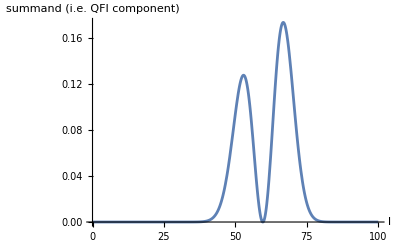

```mathematica
Block[{n=100,η=0.4},
Plot[
summand[n,l],
{l,0,n},
PlotRange->All,
AxesLabel->{"l","summand (i.e. QFI component)"}
]
]
```

```mathematica
fold data[data_]:=Table[{data[[;;,1]],data[[;;,j]]},{j,2,Dimensions[data][[2]]}]
fold data2[data_]:=Table[Transpose[{data[[;;,1]],data[[;;,j]]}],{j,2,Dimensions[data][[2]]}]
```

General::munfl: (-3.99959×10^-155)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.09958×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.19957×10^-163)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

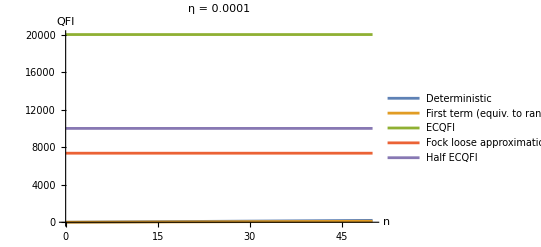

```mathematica
plot Fock[η0_]:=Block[{η=η0},
data=Table[
{n,QFI[n],prev[n],2/η,2/(η E),1/η},
{n,0,50}
];
ListPlot[
(*fold data2[data],*)
fold data2[N[data,100]],
Joined->True,
PlotRange->{0,All},
AxesLabel->{"n","QFI"},
PlotLabel->"η = "<>ToString[η],
PlotLegends->{"Deterministic","First term (equiv. to rand., small signal)","ECQFI","Fock loose approximation for rand., small signal","Half ECQFI"}
]
]
plot Fock[0.0001]
```